```mathematica
Parametric Amplification of an Optomechanical Quantum Interconnect
```

## Load the package

```mathematica
<<(NotebookDirectory[]<>"Transducer.wl");
```

## Definitions

### Define symbols

In this section we define symbols and expressions to use in this notebook.

```mathematica
<<Notation`
Symbolize[Subscript[a, _]];Symbolize[Subscript[a, _]^†];Symbolize[Subscript[Δ, _]];Symbolize[Subscript[ω, _]];Symbolize[Subscript[κ, _]];Symbolize[Subscript[G, e]];Symbolize[Subscript[G, o]];Symbolize[Subscript[g, o]];Symbolize[Subscript[g, e]];
AssumptionRealValues={Subscript[Ω, o]∈Reals,Subscript[Ω, e]∈Reals,Ω∈Reals,Subscript[ω, m]∈Reals,t∈Reals,Subscript[κ, o]∈Reals,Subscript[κ, e]∈Reals,κ∈Reals,Subscript[Δ, e]∈Reals,Subscript[Δ, o]∈Reals,Δ∈Reals,Subscript[g, e]∈Reals,Subscript[g, o]∈Reals,g∈Reals};
```

```mathematica
(*The A(t) matrix*)
A=({{-ⅈ Subscript[Δ, o]-Subscript[κ, o]/2, 0, 0, 0, -ⅈ Subscript[G, o], -ⅈ Subscript[G, o]}, {0, -ⅈ Subscript[Δ, e]-Subscript[κ, e]/2, 0, 0, -ⅈ Subscript[G, e], -ⅈ Subscript[G, e]}, {0, 0, ⅈ Subscript[Δ, o]-Subscript[κ, o]/2, 0, ⅈ Conjugate[Subscript[G, o]], ⅈ Conjugate[Subscript[G, o]]}, {0, 0, 0, ⅈ Subscript[Δ, e]-Subscript[κ, e]/2, ⅈ Conjugate[Subscript[G, e]], ⅈ Conjugate[Subscript[G, e]]}, {-ⅈ Conjugate[Subscript[G, o]], -ⅈ Conjugate[Subscript[G, e]], -ⅈ Subscript[G, o], -ⅈ Subscript[G, e], -Subscript[κ, m]/2-ⅈ Subscript[ω, m], 0}, {ⅈ Conjugate[Subscript[G, o]], ⅈ Conjugate[Subscript[G, e]], ⅈ Subscript[G, o], ⅈ Subscript[G, e], 0, -Subscript[κ, m]/2+ⅈ Subscript[ω, m]}});
(*The B matrix*)
B=({{√Subscript[κ, o,ex], √(Subscript[κ, o]-Subscript[κ, o,ex]), 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, √Subscript[κ, e,ex], √(Subscript[κ, e]-Subscript[κ, e,ex]), 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, √Subscript[κ, o,ex], √(Subscript[κ, o]-Subscript[κ, o,ex]), 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, √Subscript[κ, e,ex], √(Subscript[κ, e]-Subscript[κ, e,ex]), 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, √Subscript[κ, m], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, √Subscript[κ, m]}});

SymmetricValues={Subscript[Δ, e]->Subscript[ω, m],Subscript[Δ, o]->Subscript[ω, m],Subscript[κ, e]->κ,Subscript[κ, o]->κ,Subscript[κ, e,ex]->Subscript[κ, ex],Subscript[κ, o,ex]->Subscript[κ, ex],Subscript[κ, m,ex]->Subscript[κ, m],ω->Subscript[ω, m],Subscript[G, e]->G,Subscript[G, o]->G};
SymΩ={Subscript[Ω, e]->Ω,Subscript[Ω, o]->Ω};
```

Define utility functions.

```mathematica
StripInt[A_]:=Module[{},
If[Dimensions[A,1][[1]]==6,ArrayFlatten[{{A[[All,;;8;;2]],A[[All,9;;]]}}],A[[;; 8;;2,;;8;;2]]]];
SSum[T_]:=Total[Join[T[[;;2]],T[[4;;6]],T[[8;;]]]]/2+3*T[[7]]/2
```

Define default color schemes.

```mathematica
DefaultBlue=RGBColor[0.368417, 0.506779, 0.709798];DefaultOrange=RGBColor[0.880722, 0.611041, 0.142051];DefaultGreen=RGBColor[0.560181, 0.691569, 0.194885];
```

### Decompose A matrix into a Fourier series

```mathematica
ADcompMap=AmatDecompose[A];
Ad="diag"/.ADcompMap;
Am="G"/.ADcompMap;
Ap="G^*"/.ADcompMap;
```

```mathematica
Ad//MatrixForm
```

(-ⅈ Δ_o-κ_o/2 | 0 | 0 | 0 | 0 | 0
0 | -ⅈ Δ_e-κ_e/2 | 0 | 0 | 0 | 0
0 | 0 | ⅈ Δ_o-κ_o/2 | 0 | 0 | 0
0 | 0 | 0 | ⅈ Δ_e-κ_e/2 | 0 | 0
0 | 0 | 0 | 0 | -κ_m/2-ⅈ ω_m | 0
0 | 0 | 0 | 0 | 0 | -κ_m/2+ⅈ ω_m)

```mathematica
Am//MatrixForm
```

(0 | 0 | 0 | 0 | -ⅈ G_o | -ⅈ G_o
0 | 0 | 0 | 0 | -ⅈ G_e | -ⅈ G_e
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -ⅈ G_o | -ⅈ G_e | 0 | 0
0 | 0 | ⅈ G_o | ⅈ G_e | 0 | 0)

```mathematica
Ap//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ Conjugate[G_o] | ⅈ Conjugate[G_o]
0 | 0 | 0 | 0 | ⅈ Conjugate[G_e] | ⅈ Conjugate[G_e]
-ⅈ Conjugate[G_o] | -ⅈ Conjugate[G_e] | 0 | 0 | 0 | 0
ⅈ Conjugate[G_o] | ⅈ Conjugate[G_e] | 0 | 0 | 0 | 0)

### Solve the steady state G_i

```mathematica
SteadyGConst={Subscript[G, e]->Subscript[g, e]*SolveSteadyConst[Subscript[Δ, e], Subscript[κ, e], Subscript[Ω, e]],Subscript[G, o]->Subscript[g, o]*SolveSteadyConst[Subscript[Δ, o], Subscript[κ, o], Subscript[Ω, o]]};
SteadyGOsc={Subscript[G, e]->Subscript[g, e]*SolveSteadyOsc[Subscript[Δ, e],Subscript[κ, e],Subscript[Ω, e],Subscript[ω, m]],Subscript[G, o]->Subscript[g, o]*SolveSteadyOsc[Subscript[Δ, o],Subscript[κ, o],Subscript[Ω, o],Subscript[ω, m]]};
SteadyGConstSym = {G->g*SolveSteadyConst[Subscript[ω, m], κ, Ω]};
SteadyGOscSym={G->g*SolveSteadyOsc[Subscript[ω, m],κ,Ω,Subscript[ω, m]]};
```

The steady state G_i with constant drives.

```mathematica
SteadyGConst
```

{G_e→-(2 g_e Ω_e)/(2 Δ_e-ⅈ κ_e),G_o→-(2 g_o Ω_o)/(2 Δ_o-ⅈ κ_o)}

The steady state G_i with parametric drives.

```mathematica
SteadyGOsc
```

{G_e→-(2 g_e Ω_e)/(2 Δ_e-ⅈ κ_e-4 ω_m),G_o→-(2 g_o Ω_o)/(2 Δ_o-ⅈ κ_o-4 ω_m)}

### Define numerical values

```mathematica
HigginPaper={Subscript[κ, e]->2.5*2*π,Subscript[κ, e,ex]->2.3*2*π,Subscript[Δ, e]->1.47*2*π,Subscript[g, e]->3.8*2*π*10^-6,Subscript[κ, o]->2.1*2*π,Subscript[κ, o,ex]->1.1*2*π,Subscript[Δ, o]->1.11*2*π,Subscript[g, o]->6.6*2*π*10^-6,Subscript[κ, m]->N[11*2*π*10^-6],Subscript[ω, m]->1.4732*2*π,Subscript[κ, o,int]->2.1*2*π-1.1*2*π,Subscript[κ, e,int]->2.5*2*π-2.3*2*π};
```

## Symmetric transducer

### Solve the transfer matrices symbolically up to N=2

```mathematica
TCon=TransFConst[A, B, Subscript[ω, m], Assumptions->AssumptionRealValues];
TOsc=TransFOsc[Ad,Ap,Am,B,1,Subscript[ω, m]];
TOsc2=TransFOsc[Ad,Ap,Am,B,2,Subscript[ω, m]];
{TOscp,TOscm}=TMech[Ad,Ap,Am,B,1,Subscript[ω, m],Assumptions->AssumptionRealValues];
{TOsc2p,TOsc2m}=TMech[Ad,Ap,Am,B,2,Subscript[ω, m],Assumptions->AssumptionRealValues];
{TOsc4p,TOsc4m}=TForth[Ad,Ap,Am,B,2,Subscript[ω, m],Assumptions->AssumptionRealValues];
```

### Print out the solution

The following two blocks shows the form of the transfer matrix with/without assumptions.

```mathematica
TCon/.SymmetricValues//Simplify//MatrixForm
```

((-κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex+4 κ ω_m-4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 ⅈ G κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (4 G √κ_ex √κ_m (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 G √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
(2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ^2-ⅈ κ κ_ex+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G (κ-κ_ex) (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) κ_m^(3/2) (κ-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
-(32 ⅈ G κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (-κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex+4 κ ω_m-4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (4 G √κ_ex √κ_m (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 G √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
-(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G (κ-κ_ex) (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ^2-ⅈ κ κ_ex+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) κ_m^(3/2) (κ-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (κ κ_m (κ-2 (κ_ex+2 ⅈ ω_m)) (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m)-32 G ω_m (κ (κ_ex+4 ⅈ ω_m)+8 ω_m (-ⅈ κ_ex+2 ω_m)) Conjugate[G])/((ⅈ κ+4 ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √κ_ex κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ_m-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) (ⅈ κ+4 ω_m)+32 G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m)) Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ (κ-κ_ex) ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (4 κ √(κ-κ_ex) √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √(κ-κ_ex) κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ G κ κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ-2 (κ_ex+2 ⅈ ω_m)) (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m)-32 G ω_m (κ (κ_ex+4 ⅈ ω_m)+8 ω_m (-ⅈ κ_ex+2 ω_m)) Conjugate[G])/((ⅈ κ+4 ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √κ_ex κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ (κ-κ_ex) ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ_m-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) (ⅈ κ+4 ω_m)+32 G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m)) Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √(κ-κ_ex) √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √(κ-κ_ex) κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(4 √κ_ex √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(4 ⅈ √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √κ_ex √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(4 ⅈ √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 G κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √(κ-κ_ex) √κ_m (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 G κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √(κ-κ_ex) √κ_m (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+64 G ω_m (ⅈ κ_m+2 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(64 ⅈ G κ_m ω_m Conjugate[G])/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
(4 √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √(κ-κ_ex) κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √(κ-κ_ex) κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √κ_ex κ_m^(3/2))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 ⅈ G κ √(κ-κ_ex) κ_m^(3/2))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √κ_ex κ_m^(3/2))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 ⅈ G κ √(κ-κ_ex) κ_m^(3/2))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (64 ⅈ G κ_m ω_m Conjugate[G])/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (κ κ_m (κ-4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+64 G ω_m (-ⅈ κ_m+2 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]))

```mathematica
TCon/.SymmetricValues//Simplify//MatrixForm
```

((-κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex+4 κ ω_m-4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 ⅈ G κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (4 G √κ_ex √κ_m (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 G √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
(2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ^2-ⅈ κ κ_ex+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G (κ-κ_ex) (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) κ_m^(3/2) (κ-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
-(32 ⅈ G κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | -(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (-κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex+4 κ ω_m-4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 κ_ex ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (4 G √κ_ex √κ_m (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 G √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
-(32 G √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | -(32 ⅈ G (κ-κ_ex) (κ-4 ⅈ ω_m) ω_m Conjugate[G])/(κ (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+16 ⅈ G (κ+4 ⅈ ω_m) ω_m Conjugate[G]))/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+32 G ω_m (ⅈ κ^2-ⅈ κ κ_ex+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(32 G^2 √(κ-κ_ex) √κ_ex ω_m)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(32 ⅈ G^2 (κ-κ_ex) ω_m)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G √(κ-κ_ex) κ_m^(3/2) (κ-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (κ κ_m (κ-2 (κ_ex+2 ⅈ ω_m)) (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m)-32 G ω_m (κ (κ_ex+4 ⅈ ω_m)+8 ω_m (-ⅈ κ_ex+2 ω_m)) Conjugate[G])/((ⅈ κ+4 ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √κ_ex κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ_m-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) (ⅈ κ+4 ω_m)+32 G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m)) Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ (κ-κ_ex) ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (4 κ √(κ-κ_ex) √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √(κ-κ_ex) κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ κ_ex ω_m Conjugate[G]^2)/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 ⅈ G κ κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ-2 (κ_ex+2 ⅈ ω_m)) (κ_m-4 ⅈ ω_m) (ⅈ κ+4 ω_m)-32 G ω_m (κ (κ_ex+4 ⅈ ω_m)+8 ω_m (-ⅈ κ_ex+2 ω_m)) Conjugate[G])/((ⅈ κ+4 ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √κ_ex κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 √(κ-κ_ex) √κ_ex ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 (κ-κ_ex) ω_m Conjugate[G]^2)/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | (32 G κ √(κ-κ_ex) √κ_ex ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (32 ⅈ G κ (κ-κ_ex) ω_m Conjugate[G])/((κ-4 ⅈ ω_m) (-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)+16 G (κ-8 ⅈ ω_m) ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (κ κ_m (κ_m-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) (ⅈ κ+4 ω_m)+32 G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m)) Conjugate[G])/((κ-4 ⅈ ω_m) (κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G])) | (4 κ √(κ-κ_ex) √κ_m (ⅈ κ_m+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 ⅈ κ √(κ-κ_ex) κ_m^(3/2) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G])
(4 √κ_ex √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(4 ⅈ √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √κ_ex √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (ⅈ κ_m+4 ω_m)-128 ⅈ G ω_m^2 Conjugate[G]) | -(4 ⅈ √(κ-κ_ex) √κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 G κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √(κ-κ_ex) √κ_m (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 G κ √κ_ex √κ_m (ⅈ κ_m+4 ω_m))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √(κ-κ_ex) √κ_m (κ_m-4 ⅈ ω_m))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+64 G ω_m (ⅈ κ_m+2 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(64 ⅈ G κ_m ω_m Conjugate[G])/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
(4 √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √(κ-κ_ex) κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √κ_ex κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (4 √(κ-κ_ex) κ_m^(3/2) (ⅈ κ+4 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √κ_ex κ_m^(3/2))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 ⅈ G κ √(κ-κ_ex) κ_m^(3/2))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | -(4 ⅈ G κ √κ_ex κ_m^(3/2))/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (4 ⅈ G κ √(κ-κ_ex) κ_m^(3/2))/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]) | (64 ⅈ G κ_m ω_m Conjugate[G])/(-κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (κ κ_m (κ-4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+64 G ω_m (-ⅈ κ_m+2 ω_m) Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-128 G ω_m^2 Conjugate[G]))

```mathematica
TOsc2/.SymmetricValues//Simplify//MatrixForm
```

((-κ (κ-2 κ_ex) κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex-4 κ ω_m+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+16 G ω_m (ⅈ κ+4 ω_m) Conjugate[G]))/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | 0 | 0 | 0 | 0 | 0 | 0
(2 √(κ-κ_ex) √κ_ex (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+16 G ω_m (ⅈ κ+4 ω_m) Conjugate[G]))/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+32 ⅈ G ω_m (κ^2-κ κ_ex+4 ⅈ κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G (κ-κ_ex) (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | 0 | 0 | 0 | 0 | 0 | 0
(32 ⅈ G κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (-κ (κ-2 κ_ex) κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+32 G ω_m (ⅈ κ κ_ex-4 κ ω_m+4 κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+16 G ω_m (ⅈ κ+4 ω_m) Conjugate[G]))/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | 0 | 0 | 0 | 0 | 0 | 0
(32 ⅈ G √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (32 ⅈ G (κ-κ_ex) (κ+4 ⅈ ω_m) ω_m Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+16 G ω_m (ⅈ κ+4 ω_m) Conjugate[G]))/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | (κ (κ-2 κ_ex) κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+32 ⅈ G ω_m (κ^2-κ κ_ex+4 ⅈ κ_ex ω_m) Conjugate[G])/(κ (κ κ_m (κ+4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(ⅈ ((κ-2 (κ_ex+2 ⅈ ω_m)) (ⅈ κ^2+12 κ ω_m-32 ⅈ ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+32 G ω_m (κ (κ_ex-4 ⅈ ω_m)-16 ω_m^2) Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (κ_m^2-12 ⅈ κ_m ω_m-32 ω_m^2)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+16 ⅈ G κ ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (32 G κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (32 G √(κ-κ_ex) √κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (2 √(κ-κ_ex) √κ_ex ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+16 ⅈ G κ ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | -(ⅈ ((κ-2 κ_ex+4 ⅈ ω_m) (κ^2-12 ⅈ κ ω_m-32 ω_m^2) (ⅈ κ_m^2+12 κ_m ω_m-32 ⅈ ω_m^2)+32 G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)-16 ω_m^2) Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (κ_m^2-12 ⅈ κ_m ω_m-32 ω_m^2)+128 G ω_m^2 Conjugate[G])) | (32 G √(κ-κ_ex) √κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (32 G (κ-κ_ex) ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (32 G κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (32 G √(κ-κ_ex) √κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | ((κ-2 (κ_ex+2 ⅈ ω_m)) (ⅈ κ^2+12 κ ω_m-32 ⅈ ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+32 G ω_m (κ (κ_ex-4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/((ⅈ κ+4 ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (κ_m^2-12 ⅈ κ_m ω_m-32 ω_m^2)+128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+16 ⅈ G κ ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (32 G √(κ-κ_ex) √κ_ex ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (32 G (κ-κ_ex) ω_m (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | (2 √(κ-κ_ex) √κ_ex ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+16 ⅈ G κ ω_m Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | ((κ-2 κ_ex+4 ⅈ ω_m) (κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)+32 ⅈ G ω_m (κ^2-κ (κ_ex+4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ^2-12 ⅈ κ ω_m-32 ω_m^2) (-κ_m^2+12 ⅈ κ_m ω_m+32 ω_m^2)-128 G ω_m^2 Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)-64 ⅈ G (κ_m-2 ⅈ ω_m) ω_m Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | -(64 ⅈ G κ_m ω_m Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G])
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | (64 ⅈ G κ_m ω_m Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]) | (κ κ_m (κ-4 ⅈ ω_m) (κ_m+4 ⅈ ω_m)+64 ⅈ G (κ_m+2 ⅈ ω_m) ω_m Conjugate[G])/(κ κ_m (κ-4 ⅈ ω_m) (κ_m-4 ⅈ ω_m)+128 G ω_m^2 Conjugate[G]))

```mathematica
TCon/.SymmetricValues/.{Subscript[κ, m]->0}//Simplify//MatrixForm
```

(-1+κ_ex/κ-(ⅈ κ_ex)/(4 ω_m) | (√(κ-κ_ex) √κ_ex (-ⅈ κ+4 ω_m))/(4 κ ω_m) | -κ_ex/κ-(ⅈ κ_ex)/(4 ω_m) | -(ⅈ √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m))/(4 κ ω_m) | -(ⅈ G κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | 0 | 0
(√(κ-κ_ex) √κ_ex (-ⅈ κ+4 ω_m))/(4 κ ω_m) | -(ⅈ (κ^2-κ κ_ex-4 ⅈ κ_ex ω_m))/(4 κ ω_m) | -(ⅈ √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m))/(4 κ ω_m) | -(ⅈ (κ-κ_ex) (κ-4 ⅈ ω_m))/(4 κ ω_m) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G (κ-κ_ex))/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G (κ-κ_ex))/(4 ω_m Conjugate[G]) | 0 | 0
-κ_ex/κ-(ⅈ κ_ex)/(4 ω_m) | -(ⅈ √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m))/(4 κ ω_m) | -1+κ_ex/κ-(ⅈ κ_ex)/(4 ω_m) | (√(κ-κ_ex) √κ_ex (-ⅈ κ+4 ω_m))/(4 κ ω_m) | -(ⅈ G κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | 0 | 0
-(ⅈ √(κ-κ_ex) √κ_ex (κ-4 ⅈ ω_m))/(4 κ ω_m) | -(ⅈ (κ-κ_ex) (κ-4 ⅈ ω_m))/(4 κ ω_m) | (√(κ-κ_ex) √κ_ex (-ⅈ κ+4 ω_m))/(4 κ ω_m) | -(ⅈ (κ^2-κ κ_ex-4 ⅈ κ_ex ω_m))/(4 κ ω_m) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G (κ-κ_ex))/(4 ω_m Conjugate[G]) | -(ⅈ G √(κ-κ_ex) √κ_ex)/(4 ω_m Conjugate[G]) | -(ⅈ G (κ-κ_ex))/(4 ω_m Conjugate[G]) | 0 | 0
(ⅈ κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ κ κ_ex-4 κ ω_m+8 κ_ex ω_m+16 ⅈ ω_m^2)/(4 κ ω_m-16 ⅈ ω_m^2) | (√(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m))/(4 (κ-4 ⅈ ω_m) ω_m) | (ⅈ κ κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | (ⅈ κ √(κ-κ_ex) √κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | 0 | 0
(ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ (κ-κ_ex) Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ (κ-κ_ex) Conjugate[G])/(4 G ω_m) | (√(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m))/(4 (κ-4 ⅈ ω_m) ω_m) | -(κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m))/(4 ω_m (ⅈ κ+4 ω_m)) | (ⅈ κ √(κ-κ_ex) √κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | (ⅈ κ (κ-κ_ex))/(4 (κ-4 ⅈ ω_m) ω_m) | 0 | 0
(ⅈ κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ κ κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | (ⅈ κ √(κ-κ_ex) √κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | (ⅈ κ κ_ex-4 κ ω_m+8 κ_ex ω_m+16 ⅈ ω_m^2)/(4 κ ω_m-16 ⅈ ω_m^2) | (√(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m))/(4 (κ-4 ⅈ ω_m) ω_m) | 0 | 0
(ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ (κ-κ_ex) Conjugate[G])/(4 G ω_m) | (ⅈ √(κ-κ_ex) √κ_ex Conjugate[G])/(4 G ω_m) | (ⅈ (κ-κ_ex) Conjugate[G])/(4 G ω_m) | (ⅈ κ √(κ-κ_ex) √κ_ex)/(4 κ ω_m-16 ⅈ ω_m^2) | (ⅈ κ (κ-κ_ex))/(4 (κ-4 ⅈ ω_m) ω_m) | (√(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m))/(4 (κ-4 ⅈ ω_m) ω_m) | -(κ^2-κ (κ_ex+4 ⅈ ω_m)+8 ω_m (ⅈ κ_ex+2 ω_m))/(4 ω_m (ⅈ κ+4 ω_m)) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
TOsc/.SymmetricValues/.{Subscript[κ, m]->0}//Simplify//MatrixForm
```

(-1+κ_ex/κ | (√(κ-κ_ex) √κ_ex)/κ | -κ_ex/κ | -(√(κ-κ_ex) √κ_ex)/κ | 0 | 0 | 0 | 0 | 0 | 0
(√(κ-κ_ex) √κ_ex)/κ | -κ_ex/κ | -(√(κ-κ_ex) √κ_ex)/κ | -1+κ_ex/κ | 0 | 0 | 0 | 0 | 0 | 0
-κ_ex/κ | -(√(κ-κ_ex) √κ_ex)/κ | -1+κ_ex/κ | (√(κ-κ_ex) √κ_ex)/κ | 0 | 0 | 0 | 0 | 0 | 0
-(√(κ-κ_ex) √κ_ex)/κ | -1+κ_ex/κ | (√(κ-κ_ex) √κ_ex)/κ | -κ_ex/κ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (-((κ-2 (κ_ex+2 ⅈ ω_m)) (κ-4 ⅈ ω_m) ω_m)+G (ⅈ κ-ⅈ κ_ex+4 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 (κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | -(G κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) (ω_m (ⅈ κ+4 ω_m)+G Conjugate[G])) | (ⅈ G √(κ-κ_ex) √κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (√(κ-κ_ex) √κ_ex (2 (κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | ((κ-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) ω_m+G (ⅈ κ_ex+4 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | (ⅈ G √(κ-κ_ex) √κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | -(G (κ-κ_ex) Conjugate[G])/((κ-4 ⅈ ω_m) (ω_m (ⅈ κ+4 ω_m)+G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | -(G κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) (ω_m (ⅈ κ+4 ω_m)+G Conjugate[G])) | (ⅈ G √(κ-κ_ex) √κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | (-((κ-2 (κ_ex+2 ⅈ ω_m)) (κ-4 ⅈ ω_m) ω_m)+G (ⅈ κ-ⅈ κ_ex+4 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 (κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (ⅈ G √(κ-κ_ex) √κ_ex Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | -(G (κ-κ_ex) Conjugate[G])/((κ-4 ⅈ ω_m) (ω_m (ⅈ κ+4 ω_m)+G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 (κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G]))/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | ((κ-4 ⅈ ω_m) (κ-2 κ_ex+4 ⅈ ω_m) ω_m+G (ⅈ κ_ex+4 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ((κ-4 ⅈ ω_m) ω_m-ⅈ G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
TOsc2/.SymmetricValues/.{Subscript[κ, m]->0}//Simplify//MatrixForm
```

(-1+κ_ex/κ+(ⅈ κ_ex)/(4 ω_m) | (√(κ-κ_ex) √κ_ex (ⅈ κ+4 ω_m))/(4 κ ω_m) | -κ_ex/κ+(ⅈ κ_ex)/(4 ω_m) | (ⅈ √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m))/(4 κ ω_m) | 0 | 0 | 0 | 0 | 0 | 0
(√(κ-κ_ex) √κ_ex (ⅈ κ+4 ω_m))/(4 κ ω_m) | (ⅈ (κ^2-κ κ_ex+4 ⅈ κ_ex ω_m))/(4 κ ω_m) | (ⅈ √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m))/(4 κ ω_m) | (ⅈ (κ-κ_ex) (κ+4 ⅈ ω_m))/(4 κ ω_m) | 0 | 0 | 0 | 0 | 0 | 0
-κ_ex/κ+(ⅈ κ_ex)/(4 ω_m) | (ⅈ √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m))/(4 κ ω_m) | -1+κ_ex/κ+(ⅈ κ_ex)/(4 ω_m) | (√(κ-κ_ex) √κ_ex (ⅈ κ+4 ω_m))/(4 κ ω_m) | 0 | 0 | 0 | 0 | 0 | 0
(ⅈ √(κ-κ_ex) √κ_ex (κ+4 ⅈ ω_m))/(4 κ ω_m) | (ⅈ (κ-κ_ex) (κ+4 ⅈ ω_m))/(4 κ ω_m) | (√(κ-κ_ex) √κ_ex (ⅈ κ+4 ω_m))/(4 κ ω_m) | (ⅈ (κ^2-κ κ_ex+4 ⅈ κ_ex ω_m))/(4 κ ω_m) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | (ω_m (ⅈ κ-2 ⅈ κ_ex+4 ω_m) (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+G (κ (κ_ex-4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/(ω_m (ⅈ κ+4 ω_m) (-κ^2+12 ⅈ κ ω_m+32 ω_m^2+4 G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+ⅈ G κ Conjugate[G]))/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (G κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (G √(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (√(κ-κ_ex) √κ_ex (2 ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+ⅈ G κ Conjugate[G]))/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (ω_m (-ⅈ κ+2 ⅈ κ_ex+4 ω_m) (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+G (κ^2-κ (κ_ex+4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/(ω_m (ⅈ κ+4 ω_m) (-κ^2+12 ⅈ κ ω_m+32 ω_m^2+4 G Conjugate[G])) | (G √(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (G (κ-κ_ex) (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (G κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (G √(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (ω_m (ⅈ κ-2 ⅈ κ_ex+4 ω_m) (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+G (κ (κ_ex-4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/(ω_m (ⅈ κ+4 ω_m) (-κ^2+12 ⅈ κ ω_m+32 ω_m^2+4 G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+ⅈ G κ Conjugate[G]))/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | (G √(κ-κ_ex) √κ_ex (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (G (κ-κ_ex) (ⅈ κ+8 ω_m) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | (√(κ-κ_ex) √κ_ex (2 ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+ⅈ G κ Conjugate[G]))/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | ((κ-2 κ_ex+4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2)+ⅈ G (κ^2-κ (κ_ex+4 ⅈ ω_m)-16 ω_m^2) Conjugate[G])/((κ-4 ⅈ ω_m) ω_m (κ^2-12 ⅈ κ ω_m-32 ω_m^2-4 G Conjugate[G])) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

### Solve the transfer matrices under assumptions

```mathematica
(*Define the numerical values to be used*)
SymNValues={κ->2.5*2*π,Subscript[κ, ex]->2.5*2*π,g->3.8*2*π*10^-6,Subscript[ω, m]->1.4732*2*π,Ω->2*π*500};
(*Functions to calculate transfer matrices with constant drive*)
TConO=TCon[[1,All]]/.SymmetricValues//Simplify;
TConOSymN=Simplify[TConO/.SteadyGConstSym/.SymNValues,Assumptions->AssumptionRealValues];
SConSym[km_]:=Module[{TO,eta,S},TO=Abs[TConOSymN/.{Subscript[κ, m]->km}]^2;eta=TO[[3]];SSum[TO]/eta];
etaConSym[km_]:=Module[{TO},TO=Abs[(TConOSymN[[3]])/.{Subscript[κ, m]->km}];TO];
SConSymB[km_]:=Module[{eta,R},eta=Abs[(TConOSymN[[3]])/.{Subscript[κ, m]->km}]^2;R=Abs[(TConOSymN[[7]])/.{Subscript[κ, m]->km}]^2/eta;
Abs[(1-eta)/2/eta+R/2]+3*R/2]
(*Functions to calculate the transfer matrices with parametric drive with N = 1*)
TOscO=TOsc[[1,All]]/.SymmetricValues//Simplify;
TOscOSymN=Simplify[TOscO/.SteadyGOscSym/.SymNValues,Assumptions->AssumptionRealValues];
TOscmSymN=Simplify[TOscm[[1,All]]/.SymmetricValues/.SteadyGOscSym/.SymNValues,Assumptions->AssumptionRealValues];
SOscSym[km_]:=Module[{TO,TM,eta,S},TO=Abs[TOscOSymN/.{Subscript[κ, m]->km}]^2;TM=Abs[TOscmSymN[[10]]/.{Subscript[κ, m]->km}]^2;
eta=TO[[3]];S=SSum[TO]+TM/2;S/eta];
etaOscSym[km_]:=Module[{TO},TO=Abs[(TOscOSymN[[3]])/.{Subscript[κ, m]->km}];TO];
SOscBound[km_]:=Module[{eta},eta=etaOscSym[km];Abs[(1-eta^2)/2/eta^2]];
(*Functions to calculate the transfer matrices with parametric drive with N = 2*)
TOsc2O=TOsc2[[1,All]]/.SymmetricValues//Simplify;
TOsc2OSymN=Simplify[TOsc2O/.SteadyGOscSym/.SymNValues,Assumptions->AssumptionRealValues];
TOsc2mSymN=Simplify[TOsc2m[[1,All]]/.SymmetricValues/.SteadyGOscSym/.SymNValues,Assumptions->AssumptionRealValues];
TOsc4mSymN=Simplify[TOsc4m[[1,All]]/.SymmetricValues/.SteadyGOscSym,Assumptions->AssumptionRealValues]/.SymNValues;
SOsc2Sym[km_]:=Module[{TO,TM,T4,eta,S},TO=Abs[TOsc2OSymN/.{Subscript[κ, m]->km}]^2;TM=Abs[TOsc2mSymN[[10]]/.{Subscript[κ, m]->km}]^2;
T4=Abs[TOsc4mSymN/.{Subscript[κ, m]->km}]^2;eta=TO[[3]];S=SSum[TO]+TM/2+Total[T4]/2;
S/eta];
etaOsc2Sym[km_]:=Module[{TO},TO=Abs[(TOsc2OSymN[[3]])/.{Subscript[κ, m]->km}];TO];
SOsc2Bound[km_]:=Module[{eta},eta=etaOsc2Sym[km];Abs[(1-eta^2)/2/eta^2]];
```

### Plot the results

#### Solve for the crossing points

```mathematica
SCR=x/.FindRoot[SConSym[x]-0.5==0,{x,10^-5}];
SOR=x/.FindRoot[SOscSym[x]-0.5==0,{x,10^-5}];
SOR2=x/.FindRoot[SOsc2Sym[x]-0.5==0,{x,10^-5}];
```

#### Plotting the results (figure 2)

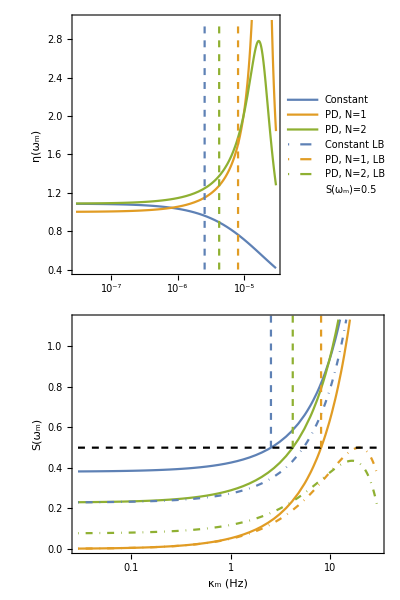

```mathematica
(*Plotting the upper panel*)
upperl=3;
lowerl=0.4;
p={{{SCR,lowerl},{SCR,upperl}},{{SOR,lowerl},{SOR,upperl}},{{SOR2,lowerl},{SOR2,upperl}}};
p2t=ListLogLinearPlot[p,Joined->True,PlotStyle->{{Dashed},{Dashed},{Dashed}}];
p1t=LogLinearPlot[{etaConSym[x],etaOscSym[x],etaOsc2Sym[x]},{x,0,3*10^-5},Ticks->{None,Automatic},BaseStyle->{FontFamily->"Times New Roman",16},PlotRange->{Automatic,{lowerl,upperl}}];
pU=Show[{p1t,p2t},ImagePadding->{{60,2},{1,6}},ImageSize->400,AspectRatio->0.618/1.5,Frame->True,FrameLabel->{Null,Row[{"η(",Subscript[ω,"m"],")"}]}];
(*Plotting the lower panel*)
upperl=3;
lowerl=0.5;
p2={{{SCR,lowerl},{SCR,upperl}},{{SOR,lowerl},{SOR,upperl}},{{SOR2,lowerl},{SOR2,upperl}}};
pd2=ListLogLinearPlot[p2,Joined->True,PlotStyle->{{Dashed},{Dashed},{Dashed}}];
pD1=LogLinearPlot[{SConSym[x],SOscSym[x],SOsc2Sym[x],SOscBound[x],SOsc2Bound[x],SConSymB[x],0.5},{x,0,3*10^-5},FrameTicks->{{0,{N[10^-7],0.1},{N[10^-6],1},{N[10^-5],10}},Automatic},BaseStyle->{FontFamily->"Times New Roman",16},PlotStyle->{Automatic,Automatic,Automatic,{DotDashed,Thick,DefaultOrange},{DotDashed,Thick,DefaultGreen},{DotDashed,Thick,DefaultBlue},{Dashed,Black}},ImagePadding->{{60,2},{45,2}},ImageSize->400,AspectRatio->0.618/1.5,Frame->True,FrameLabel->{Row[{Subscript["κ","m"], " (Hz)"}],Row[{S,"(",Subscript[ω,"m"],")"}]}];
pD=Show[{pD1,pd2}];
(*Combining figures together*)
Fig1=Multicolumn[{pU,pD},1,Spacings->{0,0}];
Fig1P=Legended[Fig1,Placed[LineLegend[{DefaultBlue,DefaultOrange,DefaultGreen,{DefaultBlue,DotDashed},{DefaultOrange,DotDashed},{DefaultGreen,DotDashed}}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"Constant","PD, N=1","PD, N=2","Constant LB","PD, N=1, LB","PD, N=2, LB",Row[{Style["S",Italic],"(", Subscript["ω","m"], ")=0.5"}]
            },LegendLayout->"Row"], Top]];
Fig1P=Legended[Fig1P,Placed[LineLegend[{Transparent}, {Style[Row[{Style[S,Italic],"(", Subscript["ω","m"], ")=0.5"}],
             FontFamily -> "Times New Roman", 14]}], {0.12,0.35}]]
```

### Solve the transfer matrix with more sidebands numerically

```mathematica
(*Set the matrices with their numerical values*)
AdN =Ad/.SymmetricValues/.SymNValues;
ApN=Ap/.SymmetricValues/.SteadyGOscSym/.SymNValues;
AmN=Am/.SymmetricValues/.SteadyGOscSym/.SymNValues;
BN=B/.SymmetricValues/.SymNValues;
(*Calculate the transfer matrix numerically*)
TOscOSym[km_,N_]:=Module[{AdNN,BNN},
AdNN=AdN/.{Subscript[κ, m]->km};
BNN=BN/.{Subscript[κ, m]->km};
TransFOsc[AdNN,ApN,AmN,BNN,N,Subscript[ω, m]/.SymNValues]
];
(*Calculate the trasduction efficiency numerically*)
etaOscNSym[km_,N_]:=Abs[TOscOSym[km,N][[1,3]]];
(*Calculate the added noise numerically*)
SOscNSym[km_,N_]:=Module[{AdNN=AdN/.{Subscript[κ, m]->km},BNN=BN/.{Subscript[κ, m]->km},w=Subscript[ω, m]/.SymNValues,T,Tp,Tm,T4p,T4m,TO,eta},
T=TransFOsc[AdNN,ApN,AmN,BNN,N,w];
T=Abs[T[[1,All]]]^2;
{Tp,Tm}=TMech[AdNN,ApN,AmN,BNN,N,w];
{T4p,T4m}=TForth[AdNN,ApN,AmN,BNN,N,w];
eta=T[[3]];
(SSum[T]+Abs[Tm[[1,10]]]^2/2+Total[Abs[T4m[[1,All]]]^2]/2)/eta
];
(*Calculate the solutions with more sidebands*)
d3=Table[{x,etaOscNSym[x,3]},{x,Logspace[-7.5,Log10[3*10^-5],200]}];
d4=Table[{x,etaOscNSym[x,4]},{x,Logspace[-7.5,Log10[3*10^-5],200]}];
d5=Table[{x,SOscNSym[x,3]},{x,Logspace[-7.5,Log10[3*10^-5],200]}];
d6=Table[{x,SOscNSym[x,4]},{x,Logspace[-7.5,Log10[3*10^-5],200]}];
```

### Plot the results with more sidebands

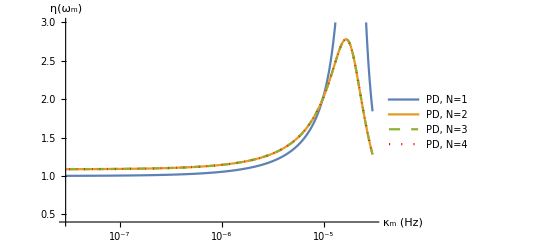

```mathematica
upperl=3;
lowerl=0.4;
p1=LogLinearPlot[{etaOscSym[x],etaOsc2Sym[x]},{x,0,3*10^-5},Ticks->{{0,{N[10^-7],0.1},{N[10^-6],1},{N[10^-5],10}},Automatic},PlotStyle->{Automatic,Automatic,{DotDashed,Thick}},BaseStyle->{FontFamily->"Times New Roman",16},AxesLabel->{Row[{Subscript["κ","m"], " (Hz)"}],Row[{"η(",Subscript[ω,"m"],")"}]},PlotRange->{Automatic,{lowerl,upperl}}];
p2=ListLogLinearPlot[{d3,d4},Joined->True,PlotStyle->{{Dashed,DefaultGreen},{Dotted,Red,Thick}}];
Ph=Show[p1,p2];
etaH=Legended[Ph,Placed[LineLegend[{DefaultBlue,DefaultOrange,{DefaultGreen,Dashed},{Red,Dotted}}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"PD, N=1","PD, N=2","PD, N=3","PD, N=4"},LegendLayout->"Row"],Top]]
```

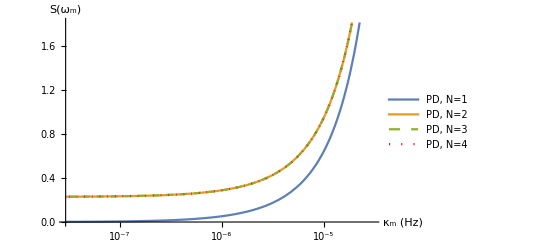

```mathematica
sp1=LogLinearPlot[{SOscSym[x],SOsc2Sym[x]},{x,0,3*10^-5},Ticks->{{0,{N[10^-7],0.1},{N[10^-6],1},{N[10^-5],10}},Automatic},BaseStyle->{FontFamily->"Times New Roman",16},AxesLabel->{Row[{Subscript["κ","m"], " (Hz)"}],Row[{S,"(",Subscript[ω,"m"],")"}]},AspectRatio->0.618];
sp2=ListLogLinearPlot[{d5,d6},Joined->True,PlotStyle->{{Dashed,DefaultGreen},{Dotted,Red,Thick}}];
spH=Show[sp1,sp2];
spH=Legended[spH,Placed[LineLegend[{DefaultBlue,DefaultOrange,{DefaultGreen,Dashed},{Red,Dotted}}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"PD, N=1","PD, N=2","PD, N=3","PD, N=4"},LegendLayout->"Row"],Top]]
```

## Realistic transducer

### Solve the transfer matrices

```mathematica
(*Functions to calculate transfer matrices with constant drive*)
TTConO=TCon[[1,All]]/.HigginPaper//Simplify;
TTConON=Simplify[TTConO/.SteadyGConst/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
SGCon[O_]:=Module[{TO,eta,S},TO=Abs[TTConON/.{Ω->O}]^2;eta=TO[[3]];SSum[TO]/eta];
etaGCon[O_]:=Module[{},Abs[(TTConON[[3]])/.{Ω->O}]];
(*Functions to calculate the transfer matrices with parametric drive with N = 1*)
TTOscO=TOsc[[1,All]]/.HigginPaper//Simplify;
TTOscON=Simplify[TTOscO/.SteadyGOsc/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
TTOscmN=Simplify[TOscm[[1,All]]/.SteadyGOsc/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
SGOsc[O_]:=Module[{TO,TM,eta},TO=Abs[TTOscON/.{Ω->O}]^2;TM=Abs[TTOscmN[[10]]/.{Ω->O}]^2;eta=TO[[3]];(SSum[TO]+TM/2)/eta];
etaGOsc[O_]:=Module[{},Abs[(TTOscON[[3]])/.{Ω->O}]];
(*Functions to calculate the transfer matrices with parametric drive with N = 2*)
TTOsc2O=TOsc2[[1,All]]/.HigginPaper//Simplify;
TTOsc2ON=Simplify[TTOsc2O/.SteadyGOsc/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
TTOsc2mN=Simplify[TOsc2m[[1,All]]/.SteadyGOsc/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
TTOsc4mN=Simplify[TOsc4m[[1,All]]/.SteadyGOsc/.HigginPaper/.SymΩ,Assumptions->AssumptionRealValues];
etaGOsc2[O_]:=Module[{},Abs[(TTOsc2ON[[3]])/.{Ω->O}]];
SGOsc2[O_]:=Module[{TO,TM,T4,eta},TO=Abs[TTOsc2ON/.{Ω->O}]^2;TM=Abs[TTOsc2mN[[10]]/.{Ω->O}]^2;
T4=Abs[TTOsc4mN/.{Ω->O}]^2;eta=TO[[3]];(SSum[TO]+TM/2+Total[T4]/2)/eta];
```

### Plot the results (figure 3)

```mathematica
(*Solve for the crossing points*)
lowerl=3;upperl=18;
C1=x/.FindRoot[Abs[SGOsc[2*π*x]-SGCon[2*π*x]]==0,{x,510}];
C2=x/.FindRoot[Abs[SGOsc2[2*π*x]-SGCon[2*π*x]]==0,{x,1050}];
p={{{C1,lowerl},{C1,upperl}},{{C2,lowerl},{C2,upperl}}};
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

```mathematica
(*Plotting the upper panel*)
```

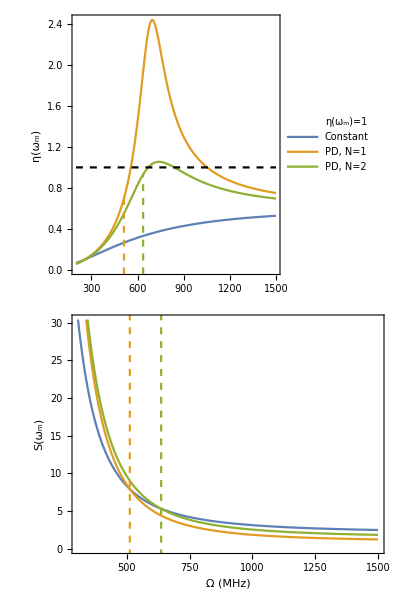

```mathematica
Sp1=Plot[{etaGCon[2*π*x],etaGOsc[2*π*x],etaGOsc2[2*π*x],1},{x,200,1500},BaseStyle->{FontFamily->"Times New Roman",16},Ticks->{None,Automatic},ImagePadding->{{60,2},{1,6}},ImageSize->400,AspectRatio->0.618/1.5,Frame->True,FrameLabel->{Null,Row[{"η(",Subscript[ω,"m"],")"}]},PlotStyle->{Automatic,Automatic,Automatic,{Dashed,Black}}];
Sp1=Legended[Sp1,Placed[LineLegend[{White}, {Style[Row[{η,"(", Subscript["ω","m"], ")=1"}],
             FontFamily -> "Times New Roman", 14]}], {0.07,0.5}]];
Sp1=Show[{Sp1,ListPlot[{{{C1,-1},{C1,etaGOsc[2*π*C1]}},{{C2,-1},{C2,etaGOsc2[2*π*C2]}}},Joined->True,PlotStyle->{{Dashed,DefaultOrange},{Dashed,DefaultGreen}}]}];
(*Plotting the lower panel*)
t=Plot[{SGCon[2*π*x],SGOsc[2*π*x],SGOsc2[2*π*x]},{x,420,760},PlotRange->{Automatic,Automatic},BaseStyle->{FontFamily->"Times New Roman",13},Ticks->{{{C1,Round[C1]},{C2,Round[C2]}},{{4,4},{8,8},{12,12}}},AspectRatio->0.618];
p2=ListPlot[p,Joined->True,PlotStyle->{{Dashed,DefaultOrange},{Dashed,DefaultGreen}}];
Sp2I=Show[{t,p2}];

Sp2F=Plot[{SGCon[2*π*x],SGOsc[2*π*x],SGOsc2[2*π*x]},{x,200,1500},PlotRange->{All,{0,Automatic}},Ticks->{None,Automatic},PlotStyle->{Automatic,Automatic,Automatic},BaseStyle->{FontFamily->"Times New Roman",16}];
Sp2F =Show[{Sp2F,ListPlot[{{{C1,-1},{C1,32}},{{C2,-1},{C2,32}}},Joined->True,PlotStyle->{{Dashed,DefaultOrange},{Dashed,DefaultGreen}}]}];
Sp2=Show[Sp2F,Epilog->Inset[Sp2I,{860,7},{480,0},{680,Automatic}],ImagePadding->{{60,2},{45,5}},ImageSize->400,AspectRatio->0.618/1.5,Frame->True,FrameLabel->{Row[{"Ω ", "(MHz)"}],Row[{S,"(",Subscript[ω,"m"],")"}]}];
(*Combining figures*)
Sp=Multicolumn[{Sp1,Sp2},1,Spacings->{0,0}];
Fig2P=Legended[Sp,Placed[LineLegend[{DefaultBlue,DefaultOrange,DefaultGreen}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"Constant","PD, N=1","PD, N=2"},LegendLayout->"Row"], Top]]
```

### Solve the transfer matrix with more sidebands numerically

```mathematica
(*Set the matrices with their numerical values*)
AdN =Ad/.HigginPaper;
ApN=Ap/.SteadyGOsc/.HigginPaper/.SymΩ;
AmN=Am/.SteadyGOsc/.HigginPaper/.SymΩ;
BN=B/.HigginPaper;
(*Calculate the transfer matrix numerically*)
TOscOG[x_,N_]:=Module[{ApNN=ApN/.{Ω->x},AmNN=AmN/.{Ω->x}},
TransFOsc[AdN,ApNN,AmNN,BN,N,Subscript[ω, m]/.HigginPaper]
];
(*Calculate the trasduction efficiency numerically*)
etaOscNG[x_,N_]:=Abs[TOscOG[x,N][[1,3]]];
(*Calculate the added noise numerically*)
SOscNG[km_,N_]:=Module[{ApNN=ApN/.{Ω->x},AmNN=AmN/.{Ω->x},w=Subscript[ω, m]/.HigginPaper,T,Tp,Tm,T4p,T4m,TO,eta},
T=TransFOsc[AdN,ApNN,AmNN,BN,N,w];
T=Abs[T[[1,All]]]^2;
{Tp,Tm}=TMech[AdN,ApNN,AmNN,BN,N,w];
{T4p,T4m}=TForth[AdN,ApNN,AmNN,BN,N,w];
eta=T[[3]];
(SSum[T]+Abs[Tm[[1,10]]]^2/2+Total[Abs[T4m[[1,All]]]^2]/2)/eta
];
di=(1500-200)/200;
d3=Table[{x/2/π,etaOscNG[x,3]},{x,2*π*200,2*π*1500}];
d4=Table[{x/2/π,etaOscNG[x,4]},{x,2*π*200,2*π*1500}];
d5=Table[{x/2/π,SOscNG[x,3]},{x,2*π*200,2*π*1500}];
d6=Table[{x/2/π,SOscNG[x,4]},{x,2*π*200,2*π*1500}];
```

### Plot the results with more sidebands

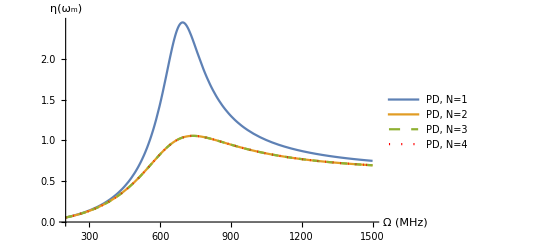

```mathematica
p1=Plot[{etaGOsc[2*π*x],etaGOsc2[2*π*x]},{x,200,1500},BaseStyle->{FontFamily->"Times New Roman",16},AxesLabel->{Row[{"Ω ", "(MHz)"}],Row[{"η(",Subscript[ω,"m"],")"}]},AspectRatio->0.618];
p2=ListPlot[{d3,d4},Joined->True,PlotStyle->{{Dashed,DefaultGreen},{Dotted,Red,Thick}}];
p=Show[p1,p2];
p=Legended[p,Placed[LineLegend[{DefaultBlue,DefaultOrange,{DefaultGreen,Dashed},{Red,Dotted}}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"PD, N=1","PD, N=2","PD, N=3","PD, N=4"},LegendLayout->"Row"],Top]]
```

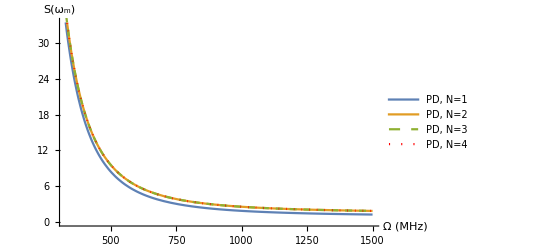

```mathematica
p1=Plot[{SGOsc[2*π*x],SGOsc2[2*π*x]},{x,200,1500},PlotRange->{All,{0,Automatic}},AxesLabel->{Row[{"Ω ", "(MHz)"}],Row[{S,"(",Subscript[ω,"m"],")"}]},BaseStyle->{FontFamily->"Times New Roman",16},AspectRatio->0.618];
p2=ListPlot[{d5,d6},Joined->True,PlotStyle->{{Dashed,DefaultGreen},{Dotted,Red,Thick}}];
p=Show[p1,p2];
p=Legended[p,Placed[LineLegend[{DefaultBlue,DefaultOrange,{DefaultGreen,Dashed},{Red,Dotted}}, Style[#,FontFamily -> "Times New Roman", 14]&/@{"PD, N=1","PD, N=2","PD, N=3","PD, N=4"},LegendLayout->"Row"],Top]]
```